```mathematica
x= 2*3
```

6

```mathematica
x
```

6

```mathematica
y = Plus[ Log[3,28],  π]
```

π+Log[28]/Log[3]

```mathematica
Pi //N
```

3.14159

NSum::itfn: π does not have the correct form for an iterator.

```mathematica
y // N
```

6.1747

```mathematica
Exp[Sqrt[y]] + 0.
```

11.9998

```mathematica
7!
```

5040

```mathematica
1/3 + 1/2
```

5/6

```mathematica
∞-∞
```

Infinity::indet: Indeterminate expression -∞+∞ encountered.

Indeterminate

```mathematica
ArcSin[Sin[15π]]
```

0

```mathematica
Round[y]
```

6

```mathematica
Round[1025,2]
```

1024

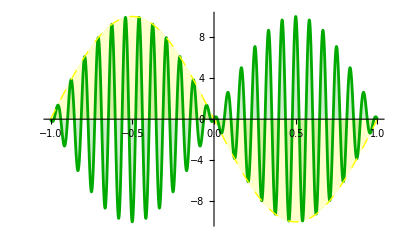

```mathematica
Plot[{10*Cos[2*π*12*t]*Sin[2*π*0.5*t], 10*Cos[2*π*0.5*t + π/2] },{t,-1,1},  Axes ->{True, False}, Filling->Axis, PlotStyle->{{Thickness[0.005], Darker[Green]},{Dashing[1/50], Yellow,  Thick}}]
```

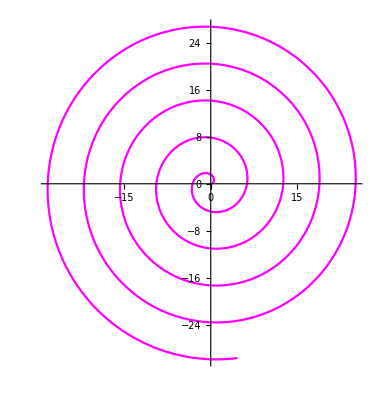

```mathematica
PolarPlot[t,{t,0,30}, PlotStyle->{Magenta}]
```

```mathematica
Plot3D[{x^2+y^2,-x^2-y^2},{x,-2,2},{y,-2,2}]
```

-Graphics3D-

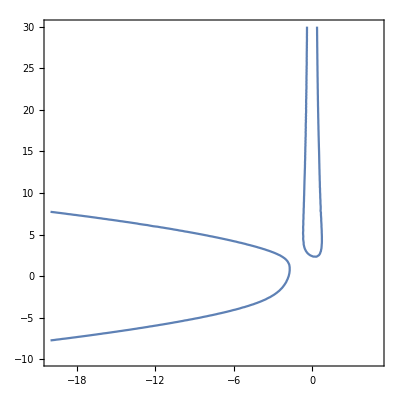

```mathematica
ContourPlot[3*x^3 +x^2*y^2-3x-5y+12==0,{x,-20,5},{y,-10,30}]
```

```mathematica
first cat curve image
```

cat curve first image

Set::write: Tag Times in Catx t is Protected.

Set::write: Tag Times in Caty t is Protected.

Set::write: Tag Times in t (π+Log[28]/Log[3]) is Protected.

```mathematica
XCat[t_]:=-(721 Sin[t])/4+196/3 Sin[2 t]-86/3 Sin[3 t]-131/2 Sin[4 t]+477/14 Sin[5 t]+27 Sin[6 t]-29/2 Sin[7 t]+68/5 Sin[8 t]+1/10 Sin[9 t]+23/4 Sin[10 t]-19/2 Sin[12 t]-85/21 Sin[13 t]+2/3 Sin[14 t]+27/5 Sin[15 t]+7/4 Sin[16 t]+17/9 Sin[17 t]-4 Sin[18 t]-1/2 Sin[19 t]+1/6 Sin[20 t]+6/7 Sin[21 t]-1/8 Sin[22 t]+1/3 Sin[23 t]+3/2 Sin[24 t]+13/5 Sin[25 t]+Sin[26 t]-2 Sin[27 t]+3/5 Sin[28 t]-1/5 Sin[29 t]+1/5 Sin[30 t]+(2337 Cos[t])/8-43/5 Cos[2 t]+322/5 Cos[3 t]-117/5 Cos[4 t]-26/5 Cos[5 t]-23/3 Cos[6 t]+143/4 Cos[7 t]-11/4 Cos[8 t]-31/3 Cos[9 t]-13/4 Cos[10 t]-9/2 Cos[11 t]+41/20 Cos[12 t]+8 Cos[13 t]+2/3 Cos[14 t]+6 Cos[15 t]+17/4 Cos[16 t]-3/2 Cos[17 t]-29/10 Cos[18 t]+11/6 Cos[19 t]+12/5 Cos[20 t]+3/2 Cos[21 t]+11/12 Cos[22 t]-4/5 Cos[23 t]+Cos[24 t]+17/8 Cos[25 t]-7/2 Cos[26 t]-5/6 Cos[27 t]-11/10 Cos[28 t]+1/2 Cos[29 t]-1/5 Cos[30 t];
```

```mathematica
YCat[t_]:=-(637 Sin[t])/2-188/5 Sin[2 t]-11/7 Sin[3 t]-12/5 Sin[4 t]+11/3 Sin[5 t]-37/4 Sin[6 t]+8/3 Sin[7 t]+65/6 Sin[8 t]-32/5 Sin[9 t]-41/4 Sin[10 t]-38/3 Sin[11 t]-47/8 Sin[12 t]+5/4 Sin[13 t]-41/7 Sin[14 t]-7/3 Sin[15 t]-13/7 Sin[16 t]+17/4 Sin[17 t]-9/4 Sin[18 t]+8/9 Sin[19 t]+3/5 Sin[20 t]-2/5 Sin[21 t]+4/3 Sin[22 t]+1/3 Sin[23 t]+3/5 Sin[24 t]-3/5 Sin[25 t]+6/5 Sin[26 t]-1/5 Sin[27 t]+10/9 Sin[28 t]+1/3 Sin[29 t]-3/4 Sin[30 t]-(125 Cos[t])/2-521/9 Cos[2 t]-359/3 Cos[3 t]+47/3 Cos[4 t]-33/2 Cos[5 t]-5/4 Cos[6 t]+31/8 Cos[7 t]+9/10 Cos[8 t]-119/4 Cos[9 t]-17/2 Cos[10 t]+22/3 Cos[11 t]+15/4 Cos[12 t]-5/2 Cos[13 t]+19/6 Cos[14 t]+7/4 Cos[15 t]+31/4 Cos[16 t]-Cos[17 t]+11/10 Cos[18 t]-2/3 Cos[19 t]+13/3 Cos[20 t]-5/4 Cos[21 t]+2/3 Cos[22 t]+1/4 Cos[23 t]+5/6 Cos[24 t]+3/4 Cos[26 t]-1/2 Cos[27 t]-1/10 Cos[28 t]-1/3 Cos[29 t]-1/19 Cos[30 t];
```

```mathematica
XCat[1] + 0.
```

65.0809

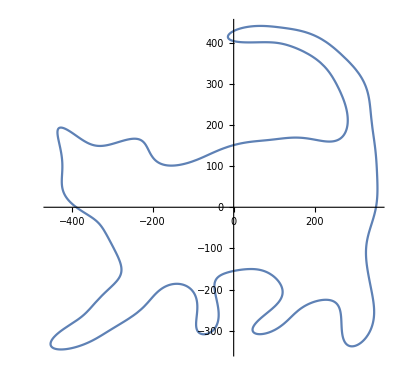

```mathematica
ParametricPlot[{XCat[t],YCat[t]},{t,0,2π}]
```

```mathematica
Sqrt[5] //N
```

2.23607

```mathematica
N[√5, 5]
```

2.2361

```mathematica
Round[Power[5, 1/2]]
```

2

```mathematica
Manipulate[Plot[{Cos[a x], Sin[b x]},{x, -10, 10}, PlotStyle->{Magenta, {Orange, Dashed }}], {a, -1, 1},{b, -1, 1}]
```